```mathematica
NullSpace[
```

```mathematica
base={"E","C","G"};
```

```mathematica
Monitor[TableForm[Table[Table[Labeled[MatrixRank[Eigenvectors[ConversionMatrix[base1,base2]]],{base1,base2}],{base1,base}],{base2,base}]],{base1,base2}]
```

$Aborted

```mathematica
ConversionMatrix["E","C"].{0,1,0,0,0,0,0,0,0,0,0,0,1,0,-3,2,1,1,-1,0,-2,0,0,-2,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
```

{0,1,0,0,0,0,0,0,0,0,0,0,1,0,-3,2,1,1,-1,0,-2,0,0,-2,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

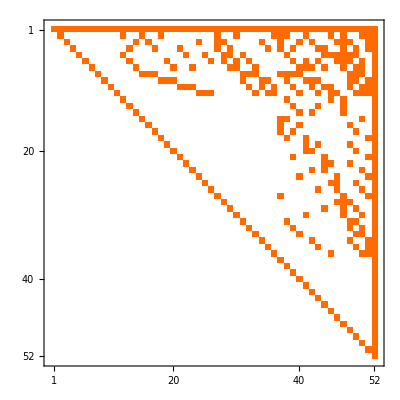

```mathematica
MatrixPlot[ConversionMatrix["E","C"]]
```

```mathematica
With[
{v=Eigenvectors[ConversionMatrix["E","C"]]},
Select[Keys[allGraphs5],MemberQ[v, BaseCoeff[#,"E"]]&]
]
```

{0}

```mathematica
DistanceFunction[
```

```mathematica
Eigenvectors[ConversionMatrix["E","G"]]
```

$Aborted

```mathematica
With[
{v=Eigenvectors[ConversionMatrix["E","C"]]},
Table[Last[First[Sort[Table[{CanberraDistance[BaseCoeff[k,"E"],ev],k},{k,Keys[allGraphs5]}]]]]
,{ev,v}
]
]
```

```mathematica
CharacteristicPolynomial[ConversionMatrix["E","C"],x]
```

1-52 x+1326 x^2-22100 x^3+270725 x^4-2598960 x^5+20358520 x^6-133784560 x^7+752538150 x^8-3679075400 x^9+15820024220 x^10-60403728840 x^11+206379406870 x^12-635013559600 x^13+1768966344600 x^14-4481381406320 x^15+10363194502115 x^16-21945588357420 x^17+42671977361650 x^18-76360380541900 x^19+125994627894135 x^20-191991813933920 x^21+270533919634160 x^22-352870329957600 x^23+426384982032100 x^24-477551179875952 x^25+495918532948104 x^26-477551179875952 x^27+426384982032100 x^28-352870329957600 x^29+270533919634160 x^30-191991813933920 x^31+125994627894135 x^32-76360380541900 x^33+42671977361650 x^34-21945588357420 x^35+10363194502115 x^36-4481381406320 x^37+1768966344600 x^38-635013559600 x^39+206379406870 x^40-60403728840 x^41+15820024220 x^42-3679075400 x^43+752538150 x^44-133784560 x^45+20358520 x^46-2598960 x^47+270725 x^48-22100 x^49+1326 x^50-52 x^51+x^52

```mathematica
Plot[1-52 x+1326 x^2-22100 x^3+270725 x^4-2598960 x^5+20358520 x^6-133784560 x^7+752538150 x^8-3679075400 x^9+15820024220 x^10-60403728840 x^11+206379406870 x^12-635013559600 x^13+1768966344600 x^14-4481381406320 x^15+10363194502115 x^16-21945588357420 x^17+42671977361650 x^18-76360380541900 x^19+125994627894135 x^20-191991813933920 x^21+270533919634160 x^22-352870329957600 x^23+426384982032100 x^24-477551179875952 x^25+495918532948104 x^26-477551179875952 x^27+426384982032100 x^28-352870329957600 x^29+270533919634160 x^30-191991813933920 x^31+125994627894135 x^32-76360380541900 x^33+42671977361650 x^34-21945588357420 x^35+10363194502115 x^36-4481381406320 x^37+1768966344600 x^38-635013559600 x^39+206379406870 x^40-60403728840 x^41+15820024220 x^42-3679075400 x^43+752538150 x^44-133784560 x^45+20358520 x^46-2598960 x^47+270725 x^48-22100 x^49+1326 x^50-52 x^51+x^52,{x,-10,10}]
```

-Graphics-

```mathematica
v=CoefficientList[CharacteristicPolynomial[ConversionMatrix["E","C"],x],x]
```

{1,-52,1326,-22100,270725,-2598960,20358520,-133784560,752538150,-3679075400,15820024220,-60403728840,206379406870,-635013559600,1768966344600,-4481381406320,10363194502115,-21945588357420,42671977361650,-76360380541900,125994627894135,-191991813933920,270533919634160,-352870329957600,426384982032100,-477551179875952,495918532948104,-477551179875952,426384982032100,-352870329957600,270533919634160,-191991813933920,125994627894135,-76360380541900,42671977361650,-21945588357420,10363194502115,-4481381406320,1768966344600,-635013559600,206379406870,-60403728840,15820024220,-3679075400,752538150,-133784560,20358520,-2598960,270725,-22100,1326,-52,1}

```mathematica
Table[(-1)^k*Binomial[52,k],{k,0,52}]
```

{1,-52,1326,-22100,270725,-2598960,20358520,-133784560,752538150,-3679075400,15820024220,-60403728840,206379406870,-635013559600,1768966344600,-4481381406320,10363194502115,-21945588357420,42671977361650,-76360380541900,125994627894135,-191991813933920,270533919634160,-352870329957600,426384982032100,-477551179875952,495918532948104,-477551179875952,426384982032100,-352870329957600,270533919634160,-191991813933920,125994627894135,-76360380541900,42671977361650,-21945588357420,10363194502115,-4481381406320,1768966344600,-635013559600,206379406870,-60403728840,15820024220,-3679075400,752538150,-133784560,20358520,-2598960,270725,-22100,1326,-52,1}

```mathematica
Length[v]
```

53

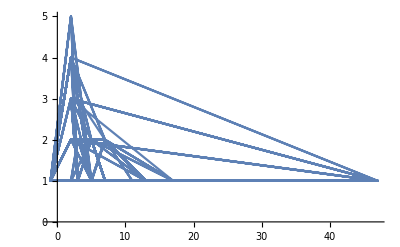

```mathematica
ListLinePlot[Flatten[FactorInteger[v],1],PlotRange->All]
```

```mathematica
v==Reverse[v]
```

True

```mathematica
FindFit[v,a x^4,{a},x]
```

{a→3.91336×10^-10}

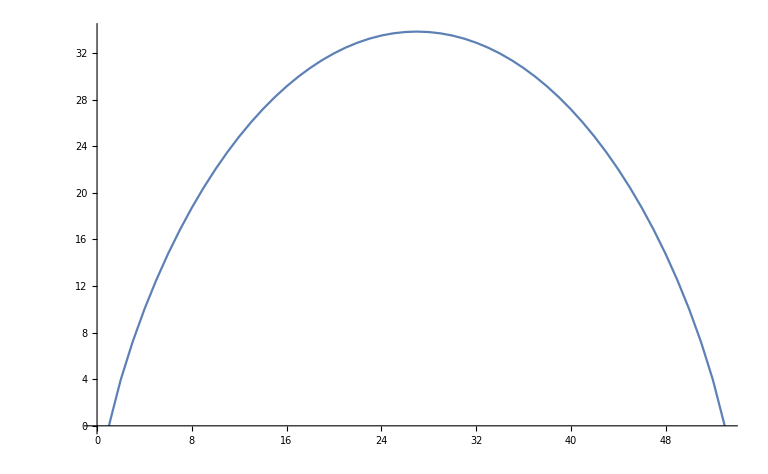

```mathematica
ListPlot[Log[Abs[v]],PlotRange->All,Joined->True]
```

```mathematica
base=allBases
```

{C,E,G,F,T}

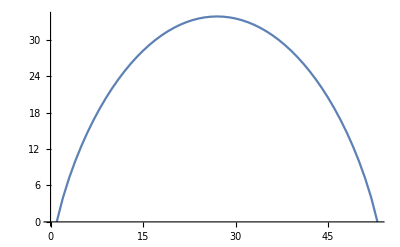
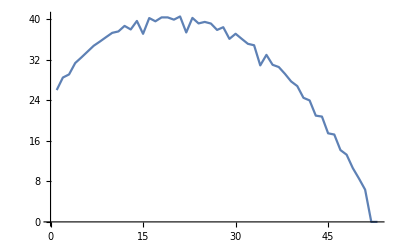
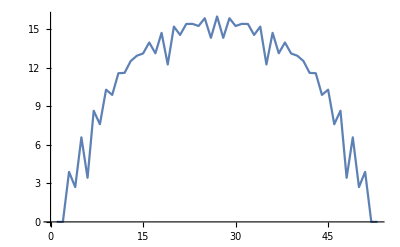
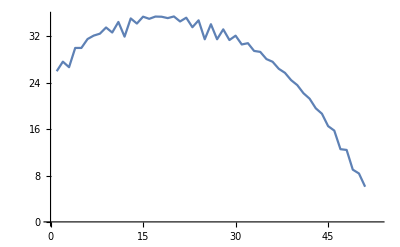
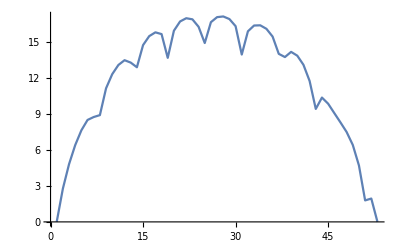
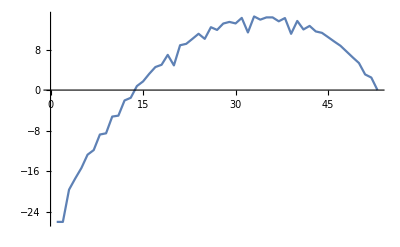
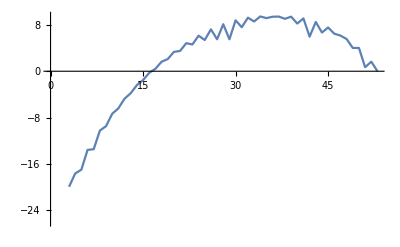
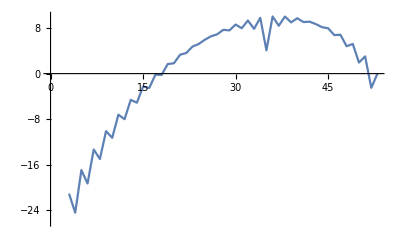
-Graphics-{C,C} | -Graphics-{E,C} | -Graphics-{G,C} | -Graphics-{F,C} | -Graphics-{T,C}
-Graphics-{C,E} | -Graphics-{E,E} | -Graphics-{G,E} | -Graphics-{F,E} | -Graphics-{T,E}
-Graphics-{C,G} | -Graphics-{E,G} | -Graphics-{G,G} | -Graphics-{F,G} | -Graphics-{T,G}
-Graphics-{C,F} | -Graphics-{E,F} | -Graphics-{G,F} | -Graphics-{F,F} | -Graphics-{T,F}
-Graphics-{C,T} | -Graphics-{E,T} | -Graphics-{G,T} | -Graphics-{F,T} | -Graphics-{T,T}

```mathematica
Monitor[TableForm[Table[Table[Labeled[With[{ch=CoefficientList[CharacteristicPolynomial[ConversionMatrix[base1,base2],x],x]},
ListPlot[Log[Abs[ch]],PlotRange->All,Joined->True]
],{base1,base2}],{base1,base}],{base2,base}]],{base1,base2}]
```

```mathematica
Monitor[TableForm[Table[Table[Labeled[With[{ch=CoefficientList[CharacteristicPolynomial[ConversionMatrix[base1,base2],x],x]},
ListPlot[Log[Abs[v]],PlotRange->All,Joined->True]
],{base1,base2}],{base1,base}],{base2,base}]],{base1,base2}]
```

-Graphics-{C,C} | -Graphics-{E,C} | -Graphics-{G,C} | -Graphics-{F,C} | -Graphics-{T,C}
-Graphics-{C,E} | -Graphics-{E,E} | -Graphics-{G,E} | -Graphics-{F,E} | -Graphics-{T,E}
-Graphics-{C,G} | -Graphics-{E,G} | -Graphics-{G,G} | -Graphics-{F,G} | -Graphics-{T,G}
-Graphics-{C,F} | -Graphics-{E,F} | -Graphics-{G,F} | -Graphics-{F,F} | -Graphics-{T,F}
-Graphics-{C,T} | -Graphics-{E,T} | -Graphics-{G,T} | -Graphics-{F,T} | -Graphics-{T,T}

```mathematica
Monitor[TableForm[Table[Table[Labeled[With[{ch=CoefficientList[CharacteristicPolynomial[ConversionMatrix[base1,base2],x],x]//N},
ch
],{base1,base2}],{base1,base}],{base2,base}]],{base1,base2}]
```

{1.,-52.,1326.,-22100.,270725.,-2.59896×10^6,2.03585×10^7,-1.33785×10^8,7.52538×10^8,-3.67908×10^9,1.582×10^10,-6.04037×10^10,2.06379×10^11,-6.35014×10^11,1.76897×10^12,-4.48138×10^12,1.03632×10^13,-2.19456×10^13,4.2672×10^13,-7.63604×10^13,1.25995×10^14,-1.91992×10^14,2.70534×10^14,-3.5287×10^14,4.26385×10^14,-4.77551×10^14,4.95919×10^14,-4.77551×10^14,4.26385×10^14,-3.5287×10^14,2.70534×10^14,-1.91992×10^14,1.25995×10^14,-7.63604×10^13,4.2672×10^13,-2.19456×10^13,1.03632×10^13,-4.48138×10^12,1.76897×10^12,-6.35014×10^11,2.06379×10^11,-6.04037×10^10,1.582×10^10,-3.67908×10^9,7.52538×10^8,-1.33785×10^8,2.03585×10^7,-2.59896×10^6,270725.,-22100.,1326.,-52.,1.}{C,C} | {1.,-52.,1326.,-22100.,270725.,-2.59896×10^6,2.03585×10^7,-1.33785×10^8,7.52538×10^8,-3.67908×10^9,1.582×10^10,-6.04037×10^10,2.06379×10^11,-6.35014×10^11,1.76897×10^12,-4.48138×10^12,1.03632×10^13,-2.19456×10^13,4.2672×10^13,-7.63604×10^13,1.25995×10^14,-1.91992×10^14,2.70534×10^14,-3.5287×10^14,4.26385×10^14,-4.77551×10^14,4.95919×10^14,-4.77551×10^14,4.26385×10^14,-3.5287×10^14,2.70534×10^14,-1.91992×10^14,1.25995×10^14,-7.63604×10^13,4.2672×10^13,-2.19456×10^13,1.03632×10^13,-4.48138×10^12,1.76897×10^12,-6.35014×10^11,2.06379×10^11,-6.04037×10^10,1.582×10^10,-3.67908×10^9,7.52538×10^8,-1.33785×10^8,2.03585×10^7,-2.59896×10^6,270725.,-22100.,1326.,-52.,1.}{E,C} | {1.,-52.,1326.,-22100.,270725.,-2.59896×10^6,2.03585×10^7,-1.33785×10^8,7.52538×10^8,-3.67908×10^9,1.582×10^10,-6.04037×10^10,2.06379×10^11,-6.35014×10^11,1.76897×10^12,-4.48138×10^12,1.03632×10^13,-2.19456×10^13,4.2672×10^13,-7.63604×10^13,1.25995×10^14,-1.91992×10^14,2.70534×10^14,-3.5287×10^14,4.26385×10^14,-4.77551×10^14,4.95919×10^14,-4.77551×10^14,4.26385×10^14,-3.5287×10^14,2.70534×10^14,-1.91992×10^14,1.25995×10^14,-7.63604×10^13,4.2672×10^13,-2.19456×10^13,1.03632×10^13,-4.48138×10^12,1.76897×10^12,-6.35014×10^11,2.06379×10^11,-6.04037×10^10,1.582×10^10,-3.67908×10^9,7.52538×10^8,-1.33785×10^8,2.03585×10^7,-2.59896×10^6,270725.,-22100.,1326.,-52.,1.}{G,C} | {-1.95689×10^11,-2.31566×10^12,-4.28207×10^12,4.04878×10^13,1.22275×10^14,-3.86917×10^14,-1.223×10^15,2.80033×10^15,6.67311×10^15,-1.55937×10^16,-2.06258×10^16,6.12698×10^16,3.04794×10^16,-1.62853×10^17,1.28801×10^16,2.88403×10^17,-1.5234×10^17,-3.29013×10^17,3.28097×10^17,2.10904×10^17,-3.95504×10^17,-1.68503×10^16,2.9714×10^17,-1.00306×10^17,-1.34623×10^17,9.77349×10^16,2.77572×10^16,-4.74072×10^16,4.76274×10^15,1.29971×10^16,-4.7558×10^15,-1.78724×10^15,1.35045×10^15,2.54617×10^13,-2.02481×10^14,2.86592×10^13,1.83947×10^13,-4.82295×10^12,-1.07815×10^12,4.30459×10^11,4.25796×10^10,-2.536×10^10,-1.2639×10^9,1.04996×10^9,3.8698×10^7,-3.04471×10^7,-1.41989×10^6,569145.,40820.,-5195.,-576.,-1.,1.}{F,C} | {1.,-52.,1326.,-22100.,270725.,-2.59896×10^6,2.03585×10^7,-1.33785×10^8,7.52538×10^8,-3.67908×10^9,1.582×10^10,-6.04037×10^10,2.06379×10^11,-6.35014×10^11,1.76897×10^12,-4.48138×10^12,1.03632×10^13,-2.19456×10^13,4.2672×10^13,-7.63604×10^13,1.25995×10^14,-1.91992×10^14,2.70534×10^14,-3.5287×10^14,4.26385×10^14,-4.77551×10^14,4.95919×10^14,-4.77551×10^14,4.26385×10^14,-3.5287×10^14,2.70534×10^14,-1.91992×10^14,1.25995×10^14,-7.63604×10^13,4.2672×10^13,-2.19456×10^13,1.03632×10^13,-4.48138×10^12,1.76897×10^12,-6.35014×10^11,2.06379×10^11,-6.04037×10^10,1.582×10^10,-3.67908×10^9,7.52538×10^8,-1.33785×10^8,2.03585×10^7,-2.59896×10^6,270725.,-22100.,1326.,-52.,1.}{T,C}
{1.,-52.,1326.,-22100.,270725.,-2.59896×10^6,2.03585×10^7,-1.33785×10^8,7.52538×10^8,-3.67908×10^9,1.582×10^10,-6.04037×10^10,2.06379×10^11,-6.35014×10^11,1.76897×10^12,-4.48138×10^12,1.03632×10^13,-2.19456×10^13,4.2672×10^13,-7.63604×10^13,1.25995×10^14,-1.91992×10^14,2.70534×10^14,-3.5287×10^14,4.26385×10^14,-4.77551×10^14,4.95919×10^14,-4.77551×10^14,4.26385×10^14,-3.5287×10^14,2.70534×10^14,-1.91992×10^14,1.25995×10^14,-7.63604×10^13,4.2672×10^13,-2.19456×10^13,1.03632×10^13,-4.48138×10^12,1.76897×10^12,-6.35014×10^11,2.06379×10^11,-6.04037×10^10,1.582×10^10,-3.67908×10^9,7.52538×10^8,-1.33785×10^8,2.03585×10^7,-2.59896×10^6,270725.,-22100.,1326.,-52.,1.}{C,E} | {1.,-52.,1326.,-22100.,270725.,-2.59896×10^6,2.03585×10^7,-1.33785×10^8,7.52538×10^8,-3.67908×10^9,1.582×10^10,-6.04037×10^10,2.06379×10^11,-6.35014×10^11,1.76897×10^12,-4.48138×10^12,1.03632×10^13,-2.19456×10^13,4.2672×10^13,-7.63604×10^13,1.25995×10^14,-1.91992×10^14,2.70534×10^14,-3.5287×10^14,4.26385×10^14,-4.77551×10^14,4.95919×10^14,-4.77551×10^14,4.26385×10^14,-3.5287×10^14,2.70534×10^14,-1.91992×10^14,1.25995×10^14,-7.63604×10^13,4.2672×10^13,-2.19456×10^13,1.03632×10^13,-4.48138×10^12,1.76897×10^12,-6.35014×10^11,2.06379×10^11,-6.04037×10^10,1.582×10^10,-3.67908×10^9,7.52538×10^8,-1.33785×10^8,2.03585×10^7,-2.59896×10^6,270725.,-22100.,1326.,-52.,1.}{E,E} | {1.,-1.,-49.,15.,720.,31.,-5711.,-1999.,29355.,19550.,-105668.,-108722.,273087.,413205.,-490915.,-1.15367×10^6,499594.,2.44664×10^6,209065.,-3.97962×10^6,-2.0818×10^6,4.8806×10^6,4.92568×10^6,-4.17503×10^6,-7.63385×10^6,1.659×10^6,8.76098×10^6,1.659×10^6,-7.63385×10^6,-4.17503×10^6,4.92568×10^6,4.8806×10^6,-2.0818×10^6,-3.97962×10^6,209065.,2.44664×10^6,499594.,-1.15367×10^6,-490915.,413205.,273087.,-108722.,-105668.,19550.,29355.,-1999.,-5711.,31.,720.,15.,-49.,-1.,1.}{G,E} | {-1.95689×10^11,1.01922×10^12,3.92738×10^11,-1.08716×10^13,1.09086×10^13,5.05566×10^13,-9.16179×10^13,-1.27728×10^14,3.71586×10^14,1.56084×10^14,-9.66038×10^14,7.6431×10^13,1.77234×10^15,-7.33724×10^14,-2.3993×10^15,1.65884×10^15,2.44432×10^15,-2.37945×10^15,-1.8743×10^15,2.49291×10^15,1.05219×10^15,-2.01005×10^15,-3.89662×10^14,1.28008×10^15,4.85776×10^13,-6.53354×10^14,4.86872×10^13,2.69608×10^14,-4.25878×10^13,-9.04151×10^13,1.98746×10^13,2.47131×10^13,-6.51157×10^12,-5.51239×10^12,1.59673×10^12,1.00329×10^12,-2.98062×10^11,-1.4871×10^11,4.21615×10^10,1.78521×10^10,-4.41659×10^9,-1.71275×10^9,3.25775×10^8,1.27587×10^8,-1.50604×10^7,-6.9605×10^6,282190.,247000.,8230.,-4250.,-431.,0.,1.}{F,E} | {1.,-52.,1326.,-22100.,270725.,-2.59896×10^6,2.03585×10^7,-1.33785×10^8,7.52538×10^8,-3.67908×10^9,1.582×10^10,-6.04037×10^10,2.06379×10^11,-6.35014×10^11,1.76897×10^12,-4.48138×10^12,1.03632×10^13,-2.19456×10^13,4.2672×10^13,-7.63604×10^13,1.25995×10^14,-1.91992×10^14,2.70534×10^14,-3.5287×10^14,4.26385×10^14,-4.77551×10^14,4.95919×10^14,-4.77551×10^14,4.26385×10^14,-3.5287×10^14,2.70534×10^14,-1.91992×10^14,1.25995×10^14,-7.63604×10^13,4.2672×10^13,-2.19456×10^13,1.03632×10^13,-4.48138×10^12,1.76897×10^12,-6.35014×10^11,2.06379×10^11,-6.04037×10^10,1.582×10^10,-3.67908×10^9,7.52538×10^8,-1.33785×10^8,2.03585×10^7,-2.59896×10^6,270725.,-22100.,1326.,-52.,1.}{T,E}
{1.,-52.,1326.,-22100.,270725.,-2.59896×10^6,2.03585×10^7,-1.33785×10^8,7.52538×10^8,-3.67908×10^9,1.582×10^10,-6.04037×10^10,2.06379×10^11,-6.35014×10^11,1.76897×10^12,-4.48138×10^12,1.03632×10^13,-2.19456×10^13,4.2672×10^13,-7.63604×10^13,1.25995×10^14,-1.91992×10^14,2.70534×10^14,-3.5287×10^14,4.26385×10^14,-4.77551×10^14,4.95919×10^14,-4.77551×10^14,4.26385×10^14,-3.5287×10^14,2.70534×10^14,-1.91992×10^14,1.25995×10^14,-7.63604×10^13,4.2672×10^13,-2.19456×10^13,1.03632×10^13,-4.48138×10^12,1.76897×10^12,-6.35014×10^11,2.06379×10^11,-6.04037×10^10,1.582×10^10,-3.67908×10^9,7.52538×10^8,-1.33785×10^8,2.03585×10^7,-2.59896×10^6,270725.,-22100.,1326.,-52.,1.}{C,G} | {1.,-1.,-49.,15.,720.,31.,-5711.,-1999.,29355.,19550.,-105668.,-108722.,273087.,413205.,-490915.,-1.15367×10^6,499594.,2.44664×10^6,209065.,-3.97962×10^6,-2.0818×10^6,4.8806×10^6,4.92568×10^6,-4.17503×10^6,-7.63385×10^6,1.659×10^6,8.76098×10^6,1.659×10^6,-7.63385×10^6,-4.17503×10^6,4.92568×10^6,4.8806×10^6,-2.0818×10^6,-3.97962×10^6,209065.,2.44664×10^6,499594.,-1.15367×10^6,-490915.,413205.,273087.,-108722.,-105668.,19550.,29355.,-1999.,-5711.,31.,720.,15.,-49.,-1.,1.}{E,G} | {1.,-52.,1326.,-22100.,270725.,-2.59896×10^6,2.03585×10^7,-1.33785×10^8,7.52538×10^8,-3.67908×10^9,1.582×10^10,-6.04037×10^10,2.06379×10^11,-6.35014×10^11,1.76897×10^12,-4.48138×10^12,1.03632×10^13,-2.19456×10^13,4.2672×10^13,-7.63604×10^13,1.25995×10^14,-1.91992×10^14,2.70534×10^14,-3.5287×10^14,4.26385×10^14,-4.77551×10^14,4.95919×10^14,-4.77551×10^14,4.26385×10^14,-3.5287×10^14,2.70534×10^14,-1.91992×10^14,1.25995×10^14,-7.63604×10^13,4.2672×10^13,-2.19456×10^13,1.03632×10^13,-4.48138×10^12,1.76897×10^12,-6.35014×10^11,2.06379×10^11,-6.04037×10^10,1.582×10^10,-3.67908×10^9,7.52538×10^8,-1.33785×10^8,2.03585×10^7,-2.59896×10^6,270725.,-22100.,1326.,-52.,1.}{G,G} | {-1.95689×10^11,1.01922×10^12,3.92738×10^11,-1.08716×10^13,1.09086×10^13,5.05566×10^13,-9.16179×10^13,-1.27728×10^14,3.71586×10^14,1.56084×10^14,-9.66038×10^14,7.6431×10^13,1.77234×10^15,-7.33724×10^14,-2.3993×10^15,1.65884×10^15,2.44432×10^15,-2.37945×10^15,-1.8743×10^15,2.49291×10^15,1.05219×10^15,-2.01005×10^15,-3.89662×10^14,1.28008×10^15,4.85776×10^13,-6.53354×10^14,4.86872×10^13,2.69608×10^14,-4.25878×10^13,-9.04151×10^13,1.98746×10^13,2.47131×10^13,-6.51157×10^12,-5.51239×10^12,1.59673×10^12,1.00329×10^12,-2.98062×10^11,-1.4871×10^11,4.21615×10^10,1.78521×10^10,-4.41659×10^9,-1.71275×10^9,3.25775×10^8,1.27587×10^8,-1.50604×10^7,-6.9605×10^6,282190.,247000.,8230.,-4250.,-431.,0.,1.}{F,G} | {1.,-16.,123.,-603.,2068.,-4906.,6263.,7343.,-68578.,222778.,-479434.,714352.,-585059.,-397110.,2.51605×10^6,-5.31455×10^6,7.28373×10^6,-6.29259×10^6,868691.,8.33409×10^6,-1.80479×10^7,2.36345×10^7,-2.15702×10^7,1.15908×10^7,2.99372×10^6,-1.70004×10^7,2.58681×10^7,-2.73958×10^7,2.20455×10^7,-1.22043×10^7,1.14497×10^6,7.94988×10^6,-1.28776×10^7,1.30886×10^7,-9.76864×10^6,5.12299×10^6,-1.2139×10^6,-928849.,1.43039×10^6,-1.04191×10^6,487682.,-126522.,-12301.,31684.,-19057.,8703.,-4002.,1796.,-611.,110.,6.,-7.,1.}{T,G}
{-5.11014×10^-12,5.11014×10^-12,2.94344×10^-9,2.65472×10^-8,-2.08596×10^-7,-2.90841×10^-6,7.25583×10^-6,0.000155589,-0.000197752,-0.00536544,0.00645869,0.129593,-0.217588,-2.1997,5.5095,24.646,-93.9994,-146.452,1034.71,-130.113,-6900.97,9133.03,24302.8,-66416.9,-24338.3,242257.,-141843.,-499439.,687944.,512579.,-1.51843×10^6,86107.2,2.02108×10^6,-1.07775×10^6,-1.67662×10^6,1.6813×10^6,778479.,-1.47378×10^6,-65819.2,832201.,-155754.,-313097.,105401.,79686.,-34100.5,-14310.,6249.68,1977.2,-624.843,-206.898,21.8819,11.8333,1.}{C,F} | {-5.11014×10^-12,0.,2.20247×10^-9,2.17181×10^-8,-4.20564×10^-8,-1.2622×10^-6,-1.44203×10^-6,0.0000355691,0.0000769605,-0.000651987,-0.00166475,0.0087524,0.0225694,-0.0912265,-0.215451,0.759931,1.52314,-5.12693,-8.15952,28.169,33.275,-126.287,-101.562,462.033,217.63,-1377.73,-248.798,3338.73,-248.238,-6541.37,1991.23,10271.6,-5376.85,-12739.1,9577.93,12159.3,-12490.8,-8476.91,12260.7,3749.43,-9056.88,-390.573,4936.58,-797.613,-1898.86,652.705,468.18,-258.351,-55.7446,55.5556,-2.00694,-5.20833,1.}{E,F} | {-5.11014×10^-12,0.,2.20247×10^-9,2.17181×10^-8,-4.20564×10^-8,-1.2622×10^-6,-1.44203×10^-6,0.0000355691,0.0000769605,-0.000651987,-0.00166475,0.0087524,0.0225694,-0.0912265,-0.215451,0.759931,1.52314,-5.12693,-8.15952,28.169,33.275,-126.287,-101.562,462.033,217.63,-1377.73,-248.798,3338.73,-248.238,-6541.37,1991.23,10271.6,-5376.85,-12739.1,9577.93,12159.3,-12490.8,-8476.91,12260.7,3749.43,-9056.88,-390.573,4936.58,-797.613,-1898.86,652.705,468.18,-258.351,-55.7446,55.5556,-2.00694,-5.20833,1.}{G,F} | {1.,-52.,1326.,-22100.,270725.,-2.59896×10^6,2.03585×10^7,-1.33785×10^8,7.52538×10^8,-3.67908×10^9,1.582×10^10,-6.04037×10^10,2.06379×10^11,-6.35014×10^11,1.76897×10^12,-4.48138×10^12,1.03632×10^13,-2.19456×10^13,4.2672×10^13,-7.63604×10^13,1.25995×10^14,-1.91992×10^14,2.70534×10^14,-3.5287×10^14,4.26385×10^14,-4.77551×10^14,4.95919×10^14,-4.77551×10^14,4.26385×10^14,-3.5287×10^14,2.70534×10^14,-1.91992×10^14,1.25995×10^14,-7.63604×10^13,4.2672×10^13,-2.19456×10^13,1.03632×10^13,-4.48138×10^12,1.76897×10^12,-6.35014×10^11,2.06379×10^11,-6.04037×10^10,1.582×10^10,-3.67908×10^9,7.52538×10^8,-1.33785×10^8,2.03585×10^7,-2.59896×10^6,270725.,-22100.,1326.,-52.,1.}{F,F} | {-5.11014×10^-12,0.,7.20529×10^-10,-2.55507×10^-11,-4.50663×10^-8,4.27719×10^-9,1.67406×10^-6,-3.14682×10^-7,-0.0000417224,0.0000129461,0.000746308,-0.000339016,-0.00999336,0.00612552,0.10301,-0.0805253,-0.832992,0.798618,5.35078,-6.12912,-27.5031,37.0563,113.388,-178.653,-373.749,692.02,974.122,-2161.28,-1958.3,5441.3,2866.99,-11001.4,-2553.4,17729.7,-59.0861,-22512.6,4432.43,22154.7,-8018.83,-16516.3,8431.27,9035.09,-5928.46,-3462.02,2839.65,863.251,-904.99,-122.39,181.35,6.97917,-20.5139,0.0833333,1.}{T,F}
{1.,-52.,1326.,-22100.,270725.,-2.59896×10^6,2.03585×10^7,-1.33785×10^8,7.52538×10^8,-3.67908×10^9,1.582×10^10,-6.04037×10^10,2.06379×10^11,-6.35014×10^11,1.76897×10^12,-4.48138×10^12,1.03632×10^13,-2.19456×10^13,4.2672×10^13,-7.63604×10^13,1.25995×10^14,-1.91992×10^14,2.70534×10^14,-3.5287×10^14,4.26385×10^14,-4.77551×10^14,4.95919×10^14,-4.77551×10^14,4.26385×10^14,-3.5287×10^14,2.70534×10^14,-1.91992×10^14,1.25995×10^14,-7.63604×10^13,4.2672×10^13,-2.19456×10^13,1.03632×10^13,-4.48138×10^12,1.76897×10^12,-6.35014×10^11,2.06379×10^11,-6.04037×10^10,1.582×10^10,-3.67908×10^9,7.52538×10^8,-1.33785×10^8,2.03585×10^7,-2.59896×10^6,270725.,-22100.,1326.,-52.,1.}{C,T} | {1.,-52.,1326.,-22100.,270725.,-2.59896×10^6,2.03585×10^7,-1.33785×10^8,7.52538×10^8,-3.67908×10^9,1.582×10^10,-6.04037×10^10,2.06379×10^11,-6.35014×10^11,1.76897×10^12,-4.48138×10^12,1.03632×10^13,-2.19456×10^13,4.2672×10^13,-7.63604×10^13,1.25995×10^14,-1.91992×10^14,2.70534×10^14,-3.5287×10^14,4.26385×10^14,-4.77551×10^14,4.95919×10^14,-4.77551×10^14,4.26385×10^14,-3.5287×10^14,2.70534×10^14,-1.91992×10^14,1.25995×10^14,-7.63604×10^13,4.2672×10^13,-2.19456×10^13,1.03632×10^13,-4.48138×10^12,1.76897×10^12,-6.35014×10^11,2.06379×10^11,-6.04037×10^10,1.582×10^10,-3.67908×10^9,7.52538×10^8,-1.33785×10^8,2.03585×10^7,-2.59896×10^6,270725.,-22100.,1326.,-52.,1.}{E,T} | {1.,-7.,6.,110.,-611.,1796.,-4002.,8703.,-19057.,31684.,-12301.,-126522.,487682.,-1.04191×10^6,1.43039×10^6,-928849.,-1.2139×10^6,5.12299×10^6,-9.76864×10^6,1.30886×10^7,-1.28776×10^7,7.94988×10^6,1.14497×10^6,-1.22043×10^7,2.20455×10^7,-2.73958×10^7,2.58681×10^7,-1.70004×10^7,2.99372×10^6,1.15908×10^7,-2.15702×10^7,2.36345×10^7,-1.80479×10^7,8.33409×10^6,868691.,-6.29259×10^6,7.28373×10^6,-5.31455×10^6,2.51605×10^6,-397110.,-585059.,714352.,-479434.,222778.,-68578.,7343.,6263.,-4906.,2068.,-603.,123.,-16.,1.}{G,T} | {-1.95689×10^11,-1.63075×10^10,4.01435×10^12,-1.36575×10^12,-3.54883×10^13,2.39504×10^13,1.77097×10^14,-1.68929×10^14,-5.55691×10^14,6.77481×10^14,1.16014×10^15,-1.76807×10^15,-1.64991×10^15,3.23207×10^15,1.5692×10^15,-4.33544×10^15,-8.6738×10^14,4.40547×10^15,1.15625×10^13,-3.46951×10^15,4.99673×10^14,2.15287×10^15,-5.61039×10^14,-1.0648×10^15,3.83219×10^14,4.22939×10^14,-1.90625×10^14,-1.35421×10^14,7.31387×10^13,3.49606×10^13,-2.21889×10^13,-7.25152×10^12,5.38206×10^12,1.1994×10^12,-1.04709×10^12,-1.56281×10^11,1.63008×10^11,1.5758×10^10,-2.0158×10^10,-1.1987×10^9,1.95559×10^9,6.63418×10^7,-1.46045×10^8,-2.53341×10^6,8.16463×10^6,61580.,-327596.,-837.,8819.,5.,-141.,0.,1.}{F,T} | {1.,-52.,1326.,-22100.,270725.,-2.59896×10^6,2.03585×10^7,-1.33785×10^8,7.52538×10^8,-3.67908×10^9,1.582×10^10,-6.04037×10^10,2.06379×10^11,-6.35014×10^11,1.76897×10^12,-4.48138×10^12,1.03632×10^13,-2.19456×10^13,4.2672×10^13,-7.63604×10^13,1.25995×10^14,-1.91992×10^14,2.70534×10^14,-3.5287×10^14,4.26385×10^14,-4.77551×10^14,4.95919×10^14,-4.77551×10^14,4.26385×10^14,-3.5287×10^14,2.70534×10^14,-1.91992×10^14,1.25995×10^14,-7.63604×10^13,4.2672×10^13,-2.19456×10^13,1.03632×10^13,-4.48138×10^12,1.76897×10^12,-6.35014×10^11,2.06379×10^11,-6.04037×10^10,1.582×10^10,-3.67908×10^9,7.52538×10^8,-1.33785×10^8,2.03585×10^7,-2.59896×10^6,270725.,-22100.,1326.,-52.,1.}{T,T}

```mathematica
Log[Abs[v]]//N
```

{0.,3.95124,7.18992,10.0033,12.5089,14.7706,16.829,18.7117,20.439,22.0259,23.4845,24.8243,26.053,27.1769,28.2014,29.131,29.9693,30.7196,31.3846,31.9665,32.4673,32.8885,33.2314,33.4971,33.6864,33.7997,33.8374,33.7997,33.6864,33.4971,33.2314,32.8885,32.4673,31.9665,31.3846,30.7196,29.9693,29.131,28.2014,27.1769,26.053,24.8243,23.4845,22.0259,20.439,18.7117,16.829,14.7706,12.5089,10.0033,7.18992,3.95124,0.}

```mathematica
Table[ShowGraph5Least[k],{k,{19685,6563,6563,19685,19685,245,19685,245,245,6563,1620,168,168,168,168,1458,4374,13122,39366,54,162,486,6,18}}]
```

{-Graphics-196858,-Graphics-65639,-Graphics-65639,-Graphics-196858,-Graphics-196858,-Graphics-2458,-Graphics-196858,-Graphics-2458,-Graphics-2458,-Graphics-65639,-Graphics-16204,-Graphics-1682,-Graphics-1682,-Graphics-1682,-Graphics-1682,-Graphics-145813,-Graphics-437410,-Graphics-1312210,-Graphics-3936613,-Graphics-5410,-Graphics-16210,-Graphics-48613,-Graphics-610,-Graphics-1813}

```mathematica
With[
{v=Eigenvectors[ConversionMatrix["E","C"]]},
Table[Last[First[Sort[Table[{BrayCurtisDistance[BaseCoeff[k,"E"],ev],k},{k,Keys[allGraphs5]}]]]]
,{ev,v}
]
]
```

{19685,6563,6563,19685,19767,245,19685,245,245,6563,1620,168,168,168,168,1458,4374,13122,39366,54,162,486,6,18,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ShowGraph5Least[39384]
```

-Graphics-393845

```mathematica
With[
{ev=First[Eigenvectors[ConversionMatrix["E","C"]]]},
Sort[Table[{ManhattanDistance[BaseCoeff[k,"E"],ev],k},{k,Keys[allGraphs5]}]]
]
```

{{14,19685},{15,2},{15,168},{15,5834},{15,13124},{15,39372},{15,39384},{16,14},{16,110},{16,245},{16,448},{16,747},{16,1467},{16,2193},{16,2918},{16,4377},{16,6077},{16,6563},{16,6723},{16,7458},{16,12407},{16,13203},{16,13232},{16,16052},{16,19697},{16,19793},{16,19928},{16,22038},{16,22601},{16,25625},1836,{82,29512},{82,29514},{84,22936},{84,27094},{84,27310},{84,28552},{84,29488},{84,29520},{86,9832},{86,22882},{86,22962},{86,28714},{86,28786},{86,29280},{86,29440},{88,9838},{88,27334},{90,9840},{100,29281},{100,29497},{102,22963},{102,27337},{102,28795},{102,29443},{102,29515},{104,9841},{104,29521},{104,29523},{124,29524}}
 |  |  |  |

## And now back

```mathematica
v
```

{1,-52,1326,-22100,270725,-2598960,20358520,-133784560,752538150,-3679075400,15820024220,-60403728840,206379406870,-635013559600,1768966344600,-4481381406320,10363194502115,-21945588357420,42671977361650,-76360380541900,125994627894135,-191991813933920,270533919634160,-352870329957600,426384982032100,-477551179875952,495918532948104,-477551179875952,426384982032100,-352870329957600,270533919634160,-191991813933920,125994627894135,-76360380541900,42671977361650,-21945588357420,10363194502115,-4481381406320,1768966344600,-635013559600,206379406870,-60403728840,15820024220,-3679075400,752538150,-133784560,20358520,-2598960,270725,-22100,1326,-52,1}

```mathematica
CoefficientList[CharacteristicPolynomial[ConversionMatrix["G","C"],x],x]
```

{1,-52,1326,-22100,270725,-2598960,20358520,-133784560,752538150,-3679075400,15820024220,-60403728840,206379406870,-635013559600,1768966344600,-4481381406320,10363194502115,-21945588357420,42671977361650,-76360380541900,125994627894135,-191991813933920,270533919634160,-352870329957600,426384982032100,-477551179875952,495918532948104,-477551179875952,426384982032100,-352870329957600,270533919634160,-191991813933920,125994627894135,-76360380541900,42671977361650,-21945588357420,10363194502115,-4481381406320,1768966344600,-635013559600,206379406870,-60403728840,15820024220,-3679075400,752538150,-133784560,20358520,-2598960,270725,-22100,1326,-52,1}

```mathematica
CoefficientList[CharacteristicPolynomial[ConversionMatrix["C","E"],x],x]
```

{1,-52,1326,-22100,270725,-2598960,20358520,-133784560,752538150,-3679075400,15820024220,-60403728840,206379406870,-635013559600,1768966344600,-4481381406320,10363194502115,-21945588357420,42671977361650,-76360380541900,125994627894135,-191991813933920,270533919634160,-352870329957600,426384982032100,-477551179875952,495918532948104,-477551179875952,426384982032100,-352870329957600,270533919634160,-191991813933920,125994627894135,-76360380541900,42671977361650,-21945588357420,10363194502115,-4481381406320,1768966344600,-635013559600,206379406870,-60403728840,15820024220,-3679075400,752538150,-133784560,20358520,-2598960,270725,-22100,1326,-52,1}

```mathematica
base={"E","C","G"}
```

{E,C,G}

```mathematica
PalindromeQ[]
```

```mathematica
Monitor[TableForm[Table[Table[Labeled[With[{ch=CoefficientList[CharacteristicPolynomial[ConversionMatrix[base1,base2],x],x]},
ch
],{base1,base2}],{base1,base}],{base2,base}]],{base1,base2}]
```

{1,-52,1326,-22100,270725,-2598960,20358520,-133784560,752538150,-3679075400,15820024220,-60403728840,206379406870,-635013559600,1768966344600,-4481381406320,10363194502115,-21945588357420,42671977361650,-76360380541900,125994627894135,-191991813933920,270533919634160,-352870329957600,426384982032100,-477551179875952,495918532948104,-477551179875952,426384982032100,-352870329957600,270533919634160,-191991813933920,125994627894135,-76360380541900,42671977361650,-21945588357420,10363194502115,-4481381406320,1768966344600,-635013559600,206379406870,-60403728840,15820024220,-3679075400,752538150,-133784560,20358520,-2598960,270725,-22100,1326,-52,1}{E,E} | {1,-52,1326,-22100,270725,-2598960,20358520,-133784560,752538150,-3679075400,15820024220,-60403728840,206379406870,-635013559600,1768966344600,-4481381406320,10363194502115,-21945588357420,42671977361650,-76360380541900,125994627894135,-191991813933920,270533919634160,-352870329957600,426384982032100,-477551179875952,495918532948104,-477551179875952,426384982032100,-352870329957600,270533919634160,-191991813933920,125994627894135,-76360380541900,42671977361650,-21945588357420,10363194502115,-4481381406320,1768966344600,-635013559600,206379406870,-60403728840,15820024220,-3679075400,752538150,-133784560,20358520,-2598960,270725,-22100,1326,-52,1}{C,E} | {1,-1,-49,15,720,31,-5711,-1999,29355,19550,-105668,-108722,273087,413205,-490915,-1153669,499594,2446641,209065,-3979615,-2081803,4880598,4925682,-4175030,-7633850,1658996,8760984,1658996,-7633850,-4175030,4925682,4880598,-2081803,-3979615,209065,2446641,499594,-1153669,-490915,413205,273087,-108722,-105668,19550,29355,-1999,-5711,31,720,15,-49,-1,1}{G,E}
{1,-52,1326,-22100,270725,-2598960,20358520,-133784560,752538150,-3679075400,15820024220,-60403728840,206379406870,-635013559600,1768966344600,-4481381406320,10363194502115,-21945588357420,42671977361650,-76360380541900,125994627894135,-191991813933920,270533919634160,-352870329957600,426384982032100,-477551179875952,495918532948104,-477551179875952,426384982032100,-352870329957600,270533919634160,-191991813933920,125994627894135,-76360380541900,42671977361650,-21945588357420,10363194502115,-4481381406320,1768966344600,-635013559600,206379406870,-60403728840,15820024220,-3679075400,752538150,-133784560,20358520,-2598960,270725,-22100,1326,-52,1}{E,C} | {1,-52,1326,-22100,270725,-2598960,20358520,-133784560,752538150,-3679075400,15820024220,-60403728840,206379406870,-635013559600,1768966344600,-4481381406320,10363194502115,-21945588357420,42671977361650,-76360380541900,125994627894135,-191991813933920,270533919634160,-352870329957600,426384982032100,-477551179875952,495918532948104,-477551179875952,426384982032100,-352870329957600,270533919634160,-191991813933920,125994627894135,-76360380541900,42671977361650,-21945588357420,10363194502115,-4481381406320,1768966344600,-635013559600,206379406870,-60403728840,15820024220,-3679075400,752538150,-133784560,20358520,-2598960,270725,-22100,1326,-52,1}{C,C} | {1,-52,1326,-22100,270725,-2598960,20358520,-133784560,752538150,-3679075400,15820024220,-60403728840,206379406870,-635013559600,1768966344600,-4481381406320,10363194502115,-21945588357420,42671977361650,-76360380541900,125994627894135,-191991813933920,270533919634160,-352870329957600,426384982032100,-477551179875952,495918532948104,-477551179875952,426384982032100,-352870329957600,270533919634160,-191991813933920,125994627894135,-76360380541900,42671977361650,-21945588357420,10363194502115,-4481381406320,1768966344600,-635013559600,206379406870,-60403728840,15820024220,-3679075400,752538150,-133784560,20358520,-2598960,270725,-22100,1326,-52,1}{G,C}
{1,-1,-49,15,720,31,-5711,-1999,29355,19550,-105668,-108722,273087,413205,-490915,-1153669,499594,2446641,209065,-3979615,-2081803,4880598,4925682,-4175030,-7633850,1658996,8760984,1658996,-7633850,-4175030,4925682,4880598,-2081803,-3979615,209065,2446641,499594,-1153669,-490915,413205,273087,-108722,-105668,19550,29355,-1999,-5711,31,720,15,-49,-1,1}{E,G} | {1,-52,1326,-22100,270725,-2598960,20358520,-133784560,752538150,-3679075400,15820024220,-60403728840,206379406870,-635013559600,1768966344600,-4481381406320,10363194502115,-21945588357420,42671977361650,-76360380541900,125994627894135,-191991813933920,270533919634160,-352870329957600,426384982032100,-477551179875952,495918532948104,-477551179875952,426384982032100,-352870329957600,270533919634160,-191991813933920,125994627894135,-76360380541900,42671977361650,-21945588357420,10363194502115,-4481381406320,1768966344600,-635013559600,206379406870,-60403728840,15820024220,-3679075400,752538150,-133784560,20358520,-2598960,270725,-22100,1326,-52,1}{C,G} | {1,-52,1326,-22100,270725,-2598960,20358520,-133784560,752538150,-3679075400,15820024220,-60403728840,206379406870,-635013559600,1768966344600,-4481381406320,10363194502115,-21945588357420,42671977361650,-76360380541900,125994627894135,-191991813933920,270533919634160,-352870329957600,426384982032100,-477551179875952,495918532948104,-477551179875952,426384982032100,-352870329957600,270533919634160,-191991813933920,125994627894135,-76360380541900,42671977361650,-21945588357420,10363194502115,-4481381406320,1768966344600,-635013559600,206379406870,-60403728840,15820024220,-3679075400,752538150,-133784560,20358520,-2598960,270725,-22100,1326,-52,1}{G,G}

```mathematica
Monitor[TableForm[Table[Table[Labeled[With[{ch=OrthogonalMatrixQ[ConversionMatrix[base1,base2]]},
ch
],{base1,base2}],{base1,base}],{base2,base}]],{base1,base2}]
```

True{E,E} | False{C,E} | False{G,E}
False{E,C} | True{C,C} | False{G,C}
False{E,G} | False{C,G} | True{G,G}

```mathematica
OrthogonalMatrixQ
```